```mathematica
(*Calculator/analyzer for paying off a loan at a faster rate, potentially minimizing interest paid*)
```

```mathematica
(*User inputs*)
%Mohela;
r1=6.8/100/12; (*Interest rate - APR - i.e. 6.8%*)
PV1=6413.01; (*Principal Value in USD*)
Payment1=98.92; (*Current Monthly Payment in USD*)

%ACS;
r2=4.233/100/12;
PV2=7610.35;
Payment2=127.09;

xSelect=10; (*Percentage of monthly bill extra per month*)
```

10

```mathematica
(*Taken from standard definition of Compounding Interest*)
NumberPayments=-Log[1-r*PV/Payment*(1/(1+x/100))]/Log[1+r];
```

```mathematica
NumberPayments1=NumberPayments/.PV->PV1/.r->r1/.Payment->Payment1;
NumberPayments2=NumberPayments/.PV->PV2/.r->r2/.Payment->Payment2;
```

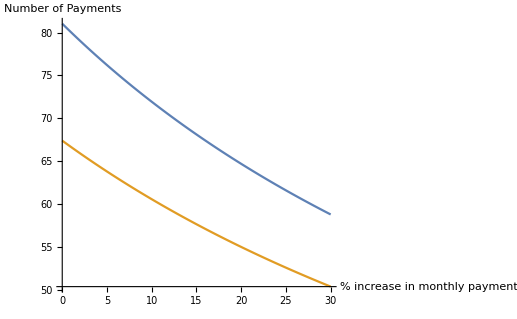

```mathematica
(*If one puts x percentage of his/her monthly bill towards the principal of the loan, he/she can pay it off y months/number of payments faster.*)
(*This plot shows this relationship*)
Plot[{NumberPayments1,NumberPayments2},{x,0,30},AxesLabel->{"% increase in monthly payment","Number of Payments"}]
```

```mathematica
TotalPaid1=NumberPayments1*Payment1*(1+x/100);
TotalPaid2=NumberPayments2*Payment2*(1+x/100);
```

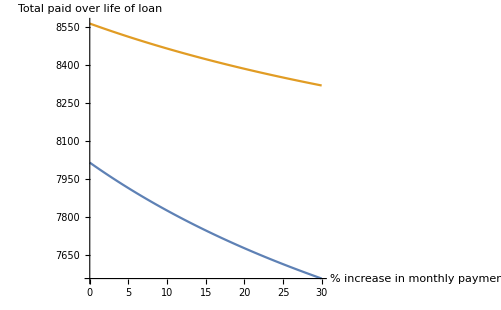

```mathematica
(*Displays the cumulative amount of money paid to creditors as a function of extra percentage added to monthly payment*)
Plot[{TotalPaid1,TotalPaid2},{x,0,30},AxesLabel->{"% increase in monthly payment","Total paid over life of loan"}]
```

```mathematica
RegularPaid1=TotalPaid1/.x->0
RegularPaid2=TotalPaid2/.x->0
```

8015.45

8564.

```mathematica
Δ1=RegularPaid1-TotalPaid1;
Δ2=RegularPaid2-TotalPaid2;
```

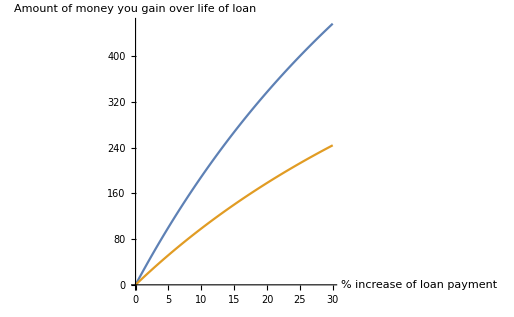

```mathematica
(*Essentially the difference one saves on interest*)
Plot[{Δ1,Δ2},{x,0,30},AxesLabel->{"% increase of loan payment","Amount of money you gain over life of loan"}]
```

```mathematica
NewPayment1=Payment1*(1+x/100)/.x->xSelect
NewPayment2=Payment2*(1+x/100)/.x->xSelect
```

108.812

139.799

```mathematica
MohelaMonthsLeft=Round[QuotientRemainder[(NumberPayments1/.x->10),12]]
ACSMonthsLeft=Round[QuotientRemainder[(NumberPayments2/.x->10),12],1]
```

{5,12}

{5,1}

```mathematica
NumberPayments1=NumberPayments/.x->xSelect/.r->r1/.Payment->Payment1/.PV->PV1-Y1
NumberPayments2=NumberPayments/.x->xSelect/.r->r2/.Payment->Payment2/.PV->PV2-(1000-Y1)
```

-176.97 Log[1-0.0000520776 (6413.01-Y1)]

-283.987 Log[1-0.0000252327 (6610.35+Y1)]

```mathematica
(*Need to revisit these sections*)
ABC=Solve[NumberPayments1==NumberPayments2,Y1]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[-176.97 Log[1-0.0000520776 (6413.01-Y1)]==-283.987 Log[1-0.0000252327 (6610.35+Y1)],Y1]

```mathematica
ABC/.Y=1000-Z
```

Set::write: Tag ReplaceAll in Solve[-176.97 Log[1-0.0000520776 Plus[«2»]]==-283.987 Log[1-0.0000252327 Plus[«2»]],Y1]/.Y is Protected.

1000-Z

```mathematica
(640+55)/2.+50+325+230+70*52/12+87+292+20+60+98
```

1812.83